```mathematica
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Miscellaneous`;
```

```mathematica
c=3*10^8;(**)
M0=(1.989*10^30 *6.674*10^-11)/c^2;(*Unitless *)
```

```mathematica
F1[Mc_,f_]:=Mc^(5/3) (f/c)^(2/3) UnitStep[1-Mc f/c]
F2[Mc_,f_]:=Mc^(5/3) (f/c)^(2/3)UnitStep[1-Mc f/c]
PDFm[Mc_,z_]:=1/Mc(*obviously fake PDF, just a placeholder*)
F1PDFm[Mc_,z_,f_]:=F1[Mc,f]PDFm[Mc,z]
F2PDFm[Mc_,z_,f_]:=F2[Mc,f]PDFm[Mc,z]
```

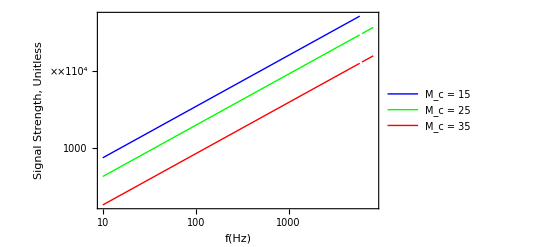

-Graphics-

```mathematica
LogLogPlot[{F1[15M0,f],F1[25M0,f],F1[35M0,f]},{f,10^1,10^3.91},AxesLabel->{Style["f(Hz)",Black,Bold,20],Style["Signal Strength, \n Unitless",Black,Bold,20]},TicksStyle->12,ImageSize->400,PlotRangePadding->.5,PlotStyle->{Red,Green,Blue},PlotLegends->Placed[LineLegend[{Blue,Green,Red},{Style["M_c = 15",Black,Bold,15],Style["M_c = 25",Black,Bold,15],Style["M_c = 35",Black,Bold,15]}],{0.85,0.35}]]

LogLogPlot[{F2[15M0,f],F2[25M0,f],F2[35M0,f]},{f,10^1,10^3.91},AxesLabel->{Style["f(Hz)",Black,Bold,20],Style["Signal Strength, \n Unitless",Black,Bold,20]},TicksStyle->12,ImageSize->400,PlotRangePadding->.5,PlotStyle->{Red,Green,Blue},PlotLegends->Placed[LineLegend[{Blue,Green,Red},{Style["M_c = 15",Black,Bold,15],Style["M_c = 25",Black,Bold,15],Style["M_c = 35",Black,Bold,15]}],{0.6,0.35}]]
```

NIntegrate::inumr: The integrand f^2/3\ Mc^2/3\ UnitStep[1 - f\ Mc/300000000]/100000\ 3^2/3\ 10^1/3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{14749.5, 73747.7}}.

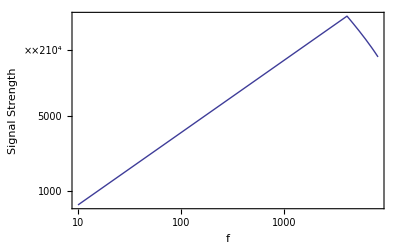

NIntegrate::inumr: The integrand f^2/3\ Mc^2/3\ UnitStep[1 - f\ Mc/300000000]/100000\ 3^2/3\ 10^1/3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{14749.5, 73747.7}}.

-Graphics-

```mathematica
LogLogPlot[NIntegrate[F1PDFm[Mc,1,f],{Mc,10 M0,50 M0}],{f,10^1,10^3.91},AxesLabel->{Style["f",Black,Bold,15],Style["Signal Strength",Black,Bold,15]},TicksStyle->15]
LogLogPlot[NIntegrate[F2PDFm[Mc,1,f],{Mc,10 M0,50 M0}],{f,10^1,10^3.91},AxesLabel->{Style["f",Black,Bold,15],Style["Signal Strength",Black,Bold,15]},TicksStyle->15]
```

```mathematica
((0.+7.739506546095161*^6 ⅈ) eta (-√(1-4 eta) Mc+(2+ⅈ √(-1+4 eta)) Mc)^(1/3) (1+1/eta^(3/5)0.00038903498955792813 f (√(1-4 eta) Mc+(-2.-(0.+1. ⅈ) √(-1+4 eta)) Mc)-(0.015381766518074116 f^(2/3) Mc (-√(1-4 eta) Mc+(2+ⅈ √(-1+4 eta)) Mc)^(2/3) ((-0.9054508748317631+1. eta-(0.+0.6554508748317631 ⅈ) √(-1+4 eta)) Mc+(0.+0.4054508748317631 ⅈ) √(1-4 eta) ((0.-1.616597510373444 ⅈ)+1. √(-1+4 eta)) Mc))/(eta^(2/5) (√(1-4 eta) Mc+(-2.-(0.+1. ⅈ) √(-1+4 eta)) Mc)^2)-(0.000958713614966269 f^(4/3) Mc^3 (-√(1-4 eta) Mc+(2+ⅈ √(-1+4 eta)) Mc)^(1/3) (√(1-4 eta) (-0.47263142542458975-(0.+0.43417477205176047 ⅈ) √(-1+4 eta)+eta (0.9452628508491795+(0.+0.22263142542458975 ⅈ) √(-1+4 eta))) Mc+(0.511088078797419+1. eta^2+(0.+0.47263142542458975 ⅈ) √(-1+4 eta)+eta (-1.8217208897650863-(0.+0.9452628508491795 ⅈ) √(-1+4 eta))) Mc))/(eta^(4/5) (√(1-4 eta) Mc+(-2.-(0.+1. ⅈ) √(-1+4 eta)) Mc)^3)))/((-ⅈ+√(-1+4 eta)) f^(5/3) Mc (-Mc+√(1-4 eta) Mc))
```

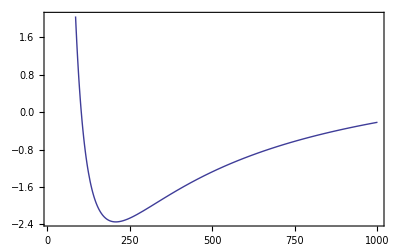

```mathematica
Plot[((2.4377918033061144*^6 (m1+m2)^2 (1-0.0007780699791158563 f (m1+m2)+0.0013802360145096144 (f (m1+m2))^(2/3) (743/336+(11 m1 m2)/(4 (m1+m2)^2))+3.857729197892504*^-6 (f (m1+m2))^(4/3) (3058673/1016064+(617 m1^2 m2^2)/(144 (m1+m2)^4)+(5429 m1 m2)/(1008 (m1+m2)^2))))/(m1 m2 (f (m1+m2))^(5/3)))/.{m1->20}/.{m2->20},{f,10,1000}]
```